### Nutrient type

{{},{},{},{}}

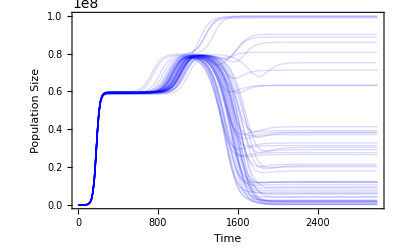

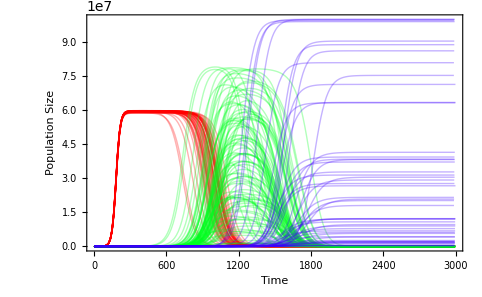

String

1/4

1/2

3/4

```mathematica
upper=1000000000;
replicate =50;

nutrientfile=ReadList["/Users/danesh/Documents/workspace/transformation/nutrient.txt",String,RecordLists->True];
locus=2;

Nut=Table[{},{m,1,2^locus}]
Nutsum={};
fr={};
counter=1;

Do[
nutrientpop={};
nutrienttype=Table[{},{n,1,2^locus}];



Do[
holdertime=ToExpression[nutrientfile[[1,counter]]];
counter++;
temp=StringDrop[nutrientfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
popnut={};
Do[
popnut=Append[popnut,ToExpression[v[[b]]]];
,{b,1,2^locus}];
nutrientpop=Append[nutrientpop,{holdertime,Total[popnut]}];


Do[
nutrienttype[[b]]=Append[nutrienttype[[b]],{holdertime,ToExpression[v[[b]]]}];
,{b,1,2^locus}];
counter++;

If[ToExpression[nutrientfile[[1,counter]]]==111111,counter++;Break[]];

,{m,1,upper}];

Nutsum=Append[Nutsum,nutrientpop];
Do[Nut[[p]]=Append[Nut[[p]],nutrienttype[[p]]];,{p,1,2^locus}];


fr=Append[fr,nutrienttype[[1]]];

,{n,1,replicate}]


Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Blue}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]



Show[Table[
Show[Table[ListPlot[Nut[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.3],Hue[StringCount[Convert[n-1,locus],"1"]/(2^(locus-1/2))]}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> All
]

String


1/2^locus
2/2^locus
3/2^locus

(*
Show[
Table[
ListPlot[nutrienttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Hue[m/2^locus],PlotRange -> All],{m,1,2^locus}]
]
ListPlot[nutrientpop,Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle -> Red]*)
```

### Fragment type

{{},{},{},{}}

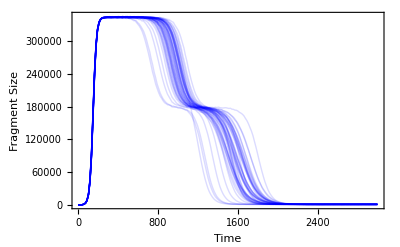

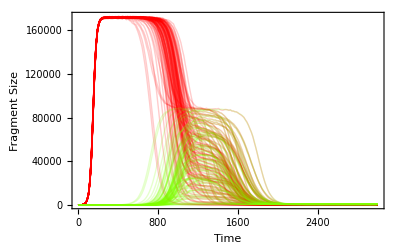

```mathematica
fragmentfile=ReadList["/Users/danesh/Documents/workspace/transformation/fragment.txt",String,RecordLists->True];
locus=2;

Frag=Table[{},{m,1,2^locus}]
Fragsum={};
fr={};
counter=1;

Do[
fragmentpop={};
fragmenttype=Table[{},{n,1,2^locus}];



Do[
holdertime=ToExpression[fragmentfile[[1,counter]]];
counter++;
temp=StringDrop[fragmentfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
popfrag={};
Do[
popfrag=Append[popfrag,ToExpression[v[[b]]]];
,{b,1,2^locus}];
fragmentpop=Append[fragmentpop,{holdertime,Total[popfrag]}];


Do[
fragmenttype[[b]]=Append[fragmenttype[[b]],{holdertime,ToExpression[v[[b]]]}];
,{b,1,2^locus}];
counter++;

If[ToExpression[fragmentfile[[1,counter]]]==111111,counter++;Break[]];

,{m,1,upper}];

Fragsum=Append[Fragsum,fragmentpop];
Do[Frag[[p]]=Append[Frag[[p]],fragmenttype[[p]]];,{p,1,2^locus}];


fr=Append[fr,fragmenttype[[1]]];

,{n,1,replicate}]


Show[Table[ListPlot[Fragsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Blue}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Fragment Size"}]



Show[Table[
Show[Table[ListPlot[Frag[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.2],Hue[StringCount[Convert[n/2,locus-1],"1"]/(2*2^(locus-1))]}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Fragment Size"},PlotRange -> All
]
```

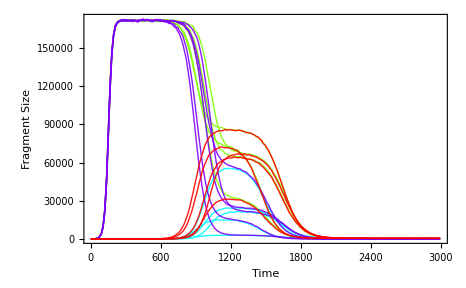
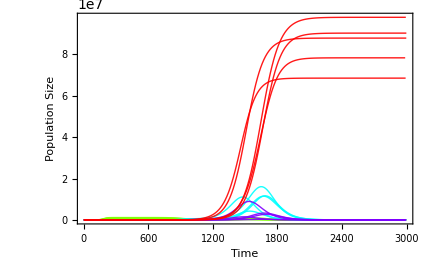

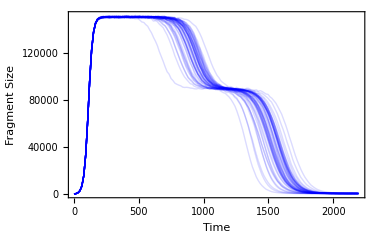
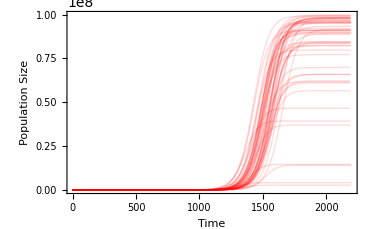
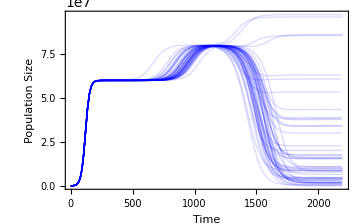

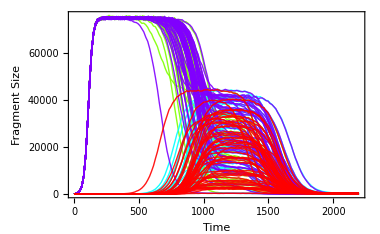

ToExpression::sntx: Invalid syntax in or before ". ".
                                                  ^

Part::partw: Part 2 of {"."} does not exist.

ToExpression::notstrbox: {"."} ⟦ 2 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Part::partw: Part 3 of {"."} does not exist.

ToExpression::notstrbox: {"."} ⟦ 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Part::partw: Part 4 of {"."} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ToExpression::notstrbox: {"."} ⟦ 4 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

ToExpression::sntx: Invalid syntax in or before "[0.0, 0.0, 0.0, 0.0]".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "[8758.0, 1.0, 8831.0, 0.0]".
                                                  ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

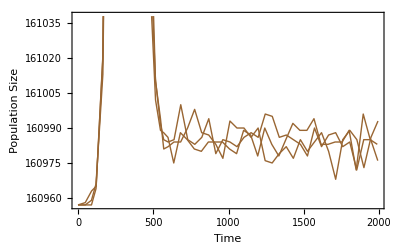

```mathematica
fragmentfile=ReadList["/Users/danesh/Documents/workspace/transformation/fragment.txt",String,RecordLists->True];

locus=2;
fragmentpop={};
counter=1;
Do[
holdertime=ToExpression[fragmentfile[[1,counter]]];
counter++;
temp=StringDrop[fragmentfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
popfrag={};
Do[
popfrag=Append[popnut,ToExpression[v[[b]]]];
,{b,1,2^locus}];
fragmentpop=Append[fragmentpop,{holdertime,Total[popfrag]}];
counter++;
,{m,1,230}]

ListPlot[fragmentpop,Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle -> Brown]
```

{{},{},{},{}}

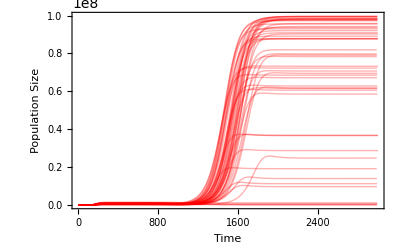

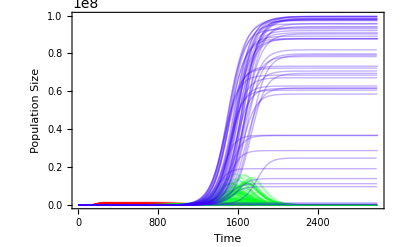

```mathematica
upper=1000000000;


recombinantfile=ReadList["/Users/danesh/Documents/workspace/transformation/recombinant.txt",String,RecordLists->True];
locus=2;

Rec=Table[{},{m,1,2^locus}]
Recsum={};
fr={};
counter=1;

Do[
recombinantpop={};
recombinanttype=Table[{},{n,1,2^locus}];



Do[
holdertime=ToExpression[recombinantfile[[1,counter]]];
counter++;
temp=StringDrop[recombinantfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
poprec={};
Do[
poprec=Append[poprec,ToExpression[v[[b]]]];
,{b,1,2^locus}];
recombinantpop=Append[recombinantpop,{holdertime,Total[poprec]}];


Do[
recombinanttype[[b]]=Append[recombinanttype[[b]],{holdertime,ToExpression[v[[b]]]}];
,{b,1,2^locus}];
counter++;

If[ToExpression[recombinantfile[[1,counter]]]==111111,counter++;Break[]];

,{m,1,upper}];

Recsum=Append[Recsum,recombinantpop];
Do[Rec[[p]]=Append[Rec[[p]],recombinanttype[[p]]];,{p,1,2^locus}];

,{n,1,replicate}]


Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.3],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]



Show[Table[
Show[Table[ListPlot[Rec[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.3],Hue[StringCount[Convert[n-1,locus],"1"]/(2^(locus-1/2))]}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> All
]






(*
Show[
Table[
ListPlot[nutrienttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Hue[m/2^locus],PlotRange -> All],{m,1,2^locus}]
]
ListPlot[nutrientpop,Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle -> Red]*)
```

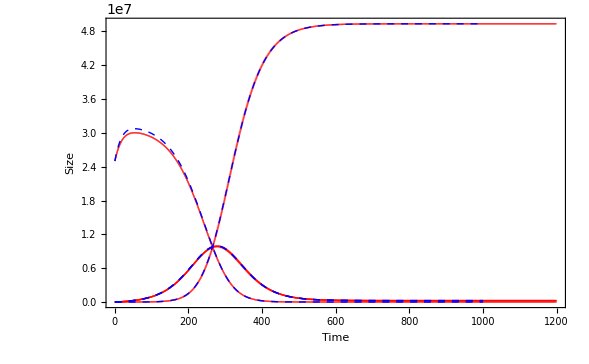

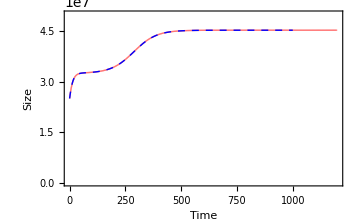

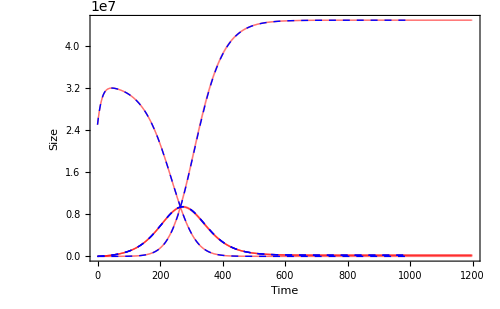

```mathematica
Show[

Show[
Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
PlotRange -> {0,50000000},AxesOrigin-> {0,0}
]
,
Plot[Evaluate[nut/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Blue,Thick,Dashed}]
,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]



Show[


Show[
Show[Table[
Show[Table[ListPlot[Nut[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Red}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> All
]
]

,
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Blue,Dashed}],{m,2^locus+1,2*2^locus}]]

,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]
```

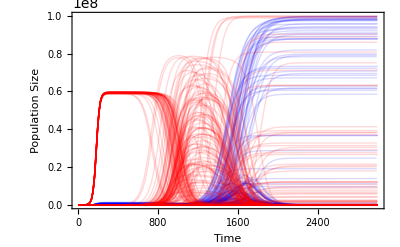

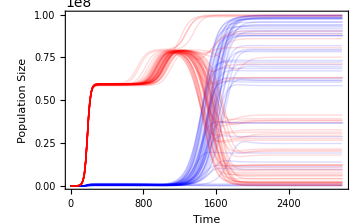

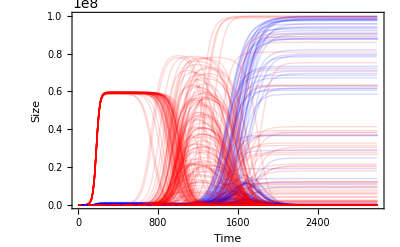

Plot::prng: Value of option PlotRange -> {0, capacity} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

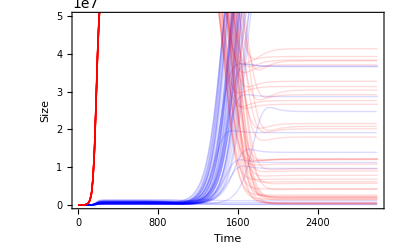

```mathematica
Show[
Show[Table[
Show[Table[ListPlot[Rec[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Blue}],{m,1,replicate}]],{n,1,2^locus}],
Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> {0,capacity}
]
,

Show[Table[
Show[Table[ListPlot[Nut[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Red}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> {0,capacity}
]
]



Show[
Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Blue}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
PlotRange -> {0,100000000},AxesOrigin-> {0,0}
]




Show[
Show[
Show[Table[
Show[Table[ListPlot[Rec[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Blue}],{m,1,replicate}]],{n,1,2^locus}],
Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> All
]
,

Show[Table[
Show[Table[ListPlot[Nut[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Red}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange ->{0,capacity}
]
]

,
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Blue,Dashed}],{m,1,2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Red,Dashed}],{m,2^locus+1,2*2^locus}]]

,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]




Show[

Show[
Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Blue}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
PlotRange -> {0,50000000},AxesOrigin-> {0,0}
]
,
Plot[Evaluate[rec/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Blue,Dashed}],
Plot[Evaluate[nut/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Red,Dashed}]
,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]
```

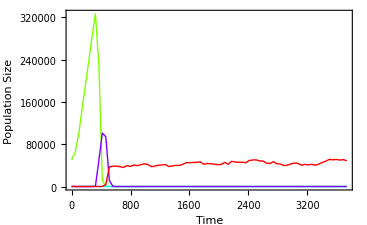

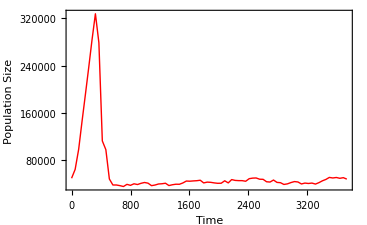

```mathematica
recombinantfile=ReadList["/Users/danesh/Documents/workspace/transformation/recombinant.txt",String,RecordLists->True];
locus=2;
recombinantpop={};
recombinanttype=Table[{},{n,1,2^locus}];
counter=1;
Do[
holdertime=ToExpression[recombinantfile[[1,counter]]];
counter++;
temp=StringDrop[recombinantfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
poprec={};
Do[
poprec=Append[poprec,ToExpression[v[[b]]]];
,{b,1,2^locus}];
recombinantpop=Append[recombinantpop,{holdertime,Total[poprec]}];

Do[
recombinanttype[[b]]=Append[recombinanttype[[b]],{holdertime,ToExpression[v[[b]]]}];
,{b,1,2^locus}];
counter++;

,{m,1,upper}]

Show[
Table[
ListPlot[recombinanttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Hue[m/2^locus],PlotRange -> All],{m,1,2^locus}]
]
ListPlot[recombinantpop,Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle -> Red]
```

### noncompetent type

{{},{},{},{}}

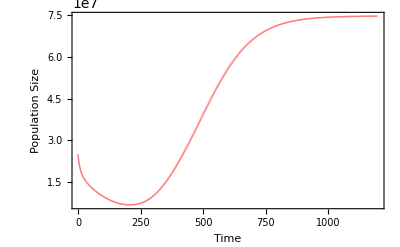

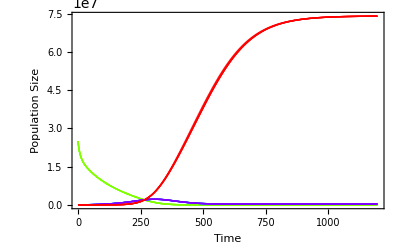

```mathematica
upper=1000000000;


noncompetentfile=ReadList["/Users/danesh/Documents/workspace/transformation/noncompetent.txt",String,RecordLists->True];
locus=2;

Non=Table[{},{m,1,2^locus}]
Nonsum={};
fr={};
counter=1;

Do[
noncompetentpop={};
noncompetenttype=Table[{},{n,1,2^locus}];



Do[
holdertime=ToExpression[noncompetentfile[[1,counter]]];
counter++;
temp=StringDrop[noncompetentfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
popnon={};
Do[
popnon=Append[popnon,ToExpression[v[[b]]]];
,{b,1,2^locus}];
noncompetentpop=Append[noncompetentpop,{holdertime,Total[popnon]}];


Do[
noncompetenttype[[b]]=Append[noncompetenttype[[b]],{holdertime,ToExpression[v[[b]]]}];
,{b,1,2^locus}];
counter++;

If[ToExpression[noncompetentfile[[1,counter]]]==111111,counter++;Break[]];

,{m,1,upper}];

Nonsum=Append[Nonsum,noncompetentpop];
Do[Non[[p]]=Append[Non[[p]],noncompetenttype[[p]]];,{p,1,2^locus}];

,{n,1,replicate}]


Show[Table[ListPlot[Nonsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]



Show[Table[
Show[Table[ListPlot[Non[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.9],Hue[n/2^locus]}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> All
]






(*
Show[
Table[
ListPlot[nutrienttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Hue[m/2^locus],PlotRange -> All],{m,1,2^locus}]
]
ListPlot[nutrientpop,Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle -> Red]*)
```

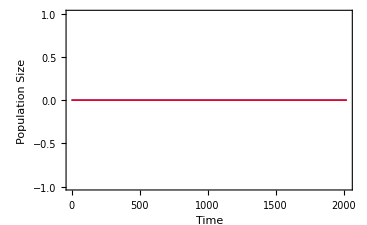

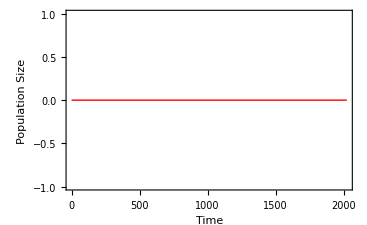

```mathematica
noncompetentfile=ReadList["/Users/danesh/Documents/workspace/transformation/noncompetent.txt",String,RecordLists->True];
locus=2;
noncompetentpop={};
noncompetenttype=Table[{},{n,1,2^locus}];
counter=1;
Do[
holdertime=ToExpression[noncompetentfile[[1,counter]]];
counter++;
temp=StringDrop[noncompetentfile[[1,counter]],1];
temp=StringDrop[temp,-1];
v=StringSplit[temp,","];
popnon={};
Do[
popnon=Append[popnon,ToExpression[v[[b]]]];
,{b,1,2^locus}];
noncompetentpop=Append[noncompetentpop,{holdertime,Total[popnon]}];

Do[
noncompetenttype[[b]]=Append[noncompetenttype[[b]],{holdertime,ToExpression[v[[b]]]}];
,{b,1,2^locus}];
counter++;

,{m,1,upper}]

Show[
Table[
ListPlot[noncompetenttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Hue[m/2^locus],PlotRange -> All],{m,1,2^locus}]
]
ListPlot[noncompetentpop,Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle -> Red]
```

plotting all three together

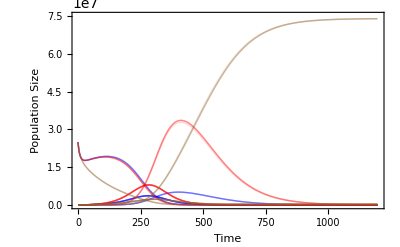

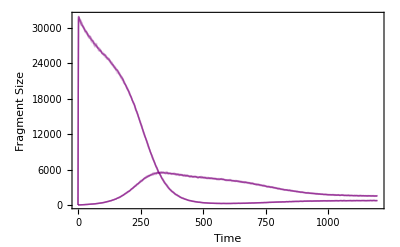

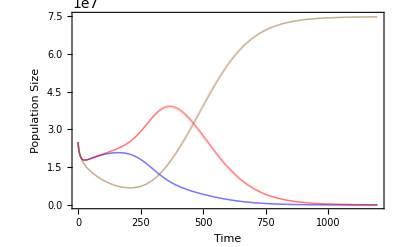

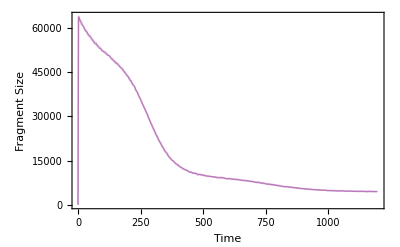

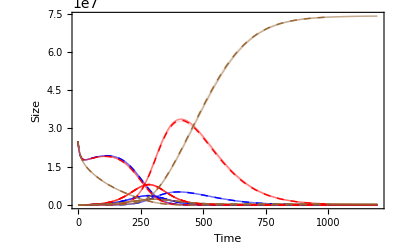

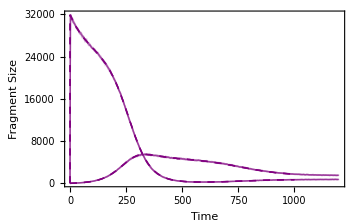

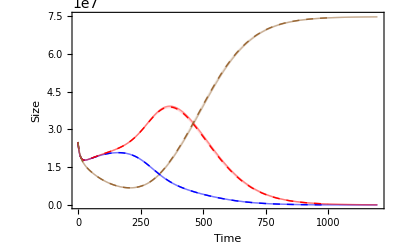

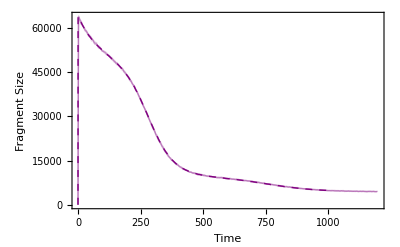

```mathematica
capacity=75000000;

Show[
Show[Table[
Show[Table[ListPlot[Rec[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Blue}],{m,1,replicate}]],{n,1,2^locus}],
Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> {0,capacity}
]
,

Show[Table[
Show[Table[ListPlot[Nut[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Red}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> {0,capacity}
]
,
Show[Table[
Show[Table[ListPlot[Non[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Brown}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> {0,capacity}
]
]


Show[Table[
Show[Table[ListPlot[Frag[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Purple}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Fragment Size"},PlotRange -> All
]



Show[
Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Blue}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Nonsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Brown}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]

,
PlotRange -> {0,capacity},AxesOrigin-> {0,0}
]


Show[Table[ListPlot[Fragsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Purple}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Fragment Size"}]








Show[
Show[
Show[Table[
Show[Table[ListPlot[Rec[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Blue}],{m,1,replicate}]],{n,1,2^locus}],
Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange -> All
]
,

Show[Table[
Show[Table[ListPlot[Nut[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Red}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange ->{0,capacity}
]


,

Show[Table[
Show[Table[ListPlot[Non[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.15],Brown}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotRange ->{0,capacity}
]


]

,
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Blue,Dashed}],{m,1,2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Red,Dashed}],{m,2^locus+1,2*2^locus}]],
Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Brown,Dashed}],{m,2*2^locus+1,3*2^locus}]]

,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]




Show[
Show[Table[
Show[Table[ListPlot[Frag[[n]][[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Purple}],{m,1,replicate}]]

,{n,1,2^locus}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Fragment Size"},PlotRange -> All
]
,
Show[Show[Table[Plot[Evaluate[ffunction[[m]] /. sol3],{t,0,g}, PlotRange->All, PlotStyle ->{Purple,Dashed}],{m,3*2^locus+1,3*2^locus+2^dnasize*(locus-dnasize+1)}]],
Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]


]









Show[

Show[
Show[Table[ListPlot[Recsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Blue}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Nutsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Red}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
Show[Table[ListPlot[Nonsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Brown}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"}]
,
PlotRange -> {0,capacity},AxesOrigin-> {0,0}
]
,
Plot[Evaluate[rec/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Blue,Dashed}],
Plot[Evaluate[nut/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Red,Dashed}],
Plot[Evaluate[non/. sol3],{t,0,g}, PlotRange->{0,capacity}, PlotStyle -> {Brown,Dashed}]
,Frame -> True,FrameStyle -> 18,FrameLabel->{"Time","Size"}
]





Show[

Show[Table[ListPlot[Fragsum[[m]], Joined -> True,PlotStyle -> {Opacity[0.14],Purple}],{m,1,replicate}],Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Fragment Size"}]

,

Plot[Evaluate[sumf/. sol3],{t,0,g}, PlotRange->All, PlotStyle -> {Purple,Dashed}]
]
```

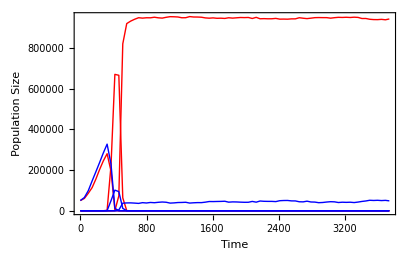

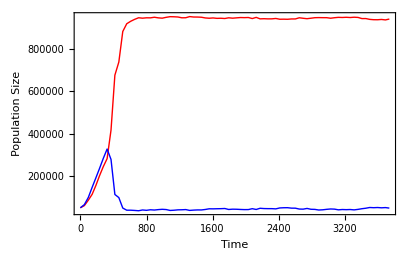

```mathematica
Show[
Show[
Table[
ListPlot[nutrienttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Red,PlotRange -> All],{m,1,2^locus}]
]
,
Show[
Table[
ListPlot[recombinanttype[[m]],Joined -> True,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},PlotStyle ->Blue,PlotRange -> All],{m,1,2^locus}]
]
]

Show[ListPlot[nutrientpop,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},Joined -> True,PlotStyle -> Red],ListPlot[recombinantpop,Frame -> True,LabelStyle -> 18,FrameLabel -> {"Time","Population Size"},Joined -> True,PlotStyle -> Blue]
]
```

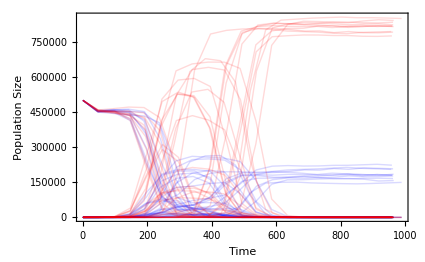

```mathematica
For deterministic model 
Estimation of parameters from loiterature 
study the behaviour of system in mutual competitions betwen non competent and competent types
```

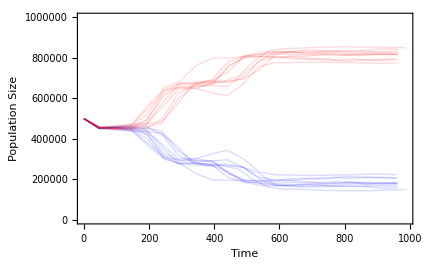
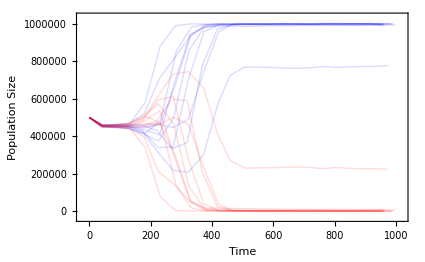

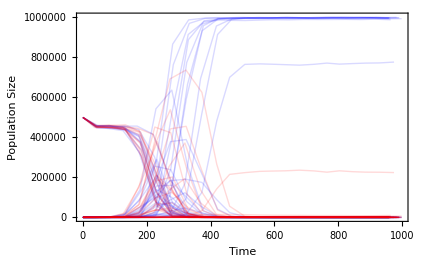

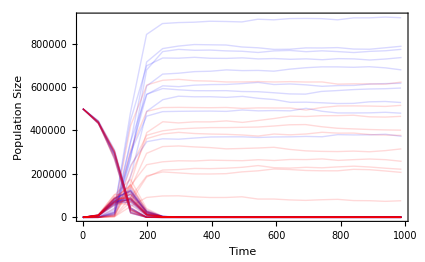

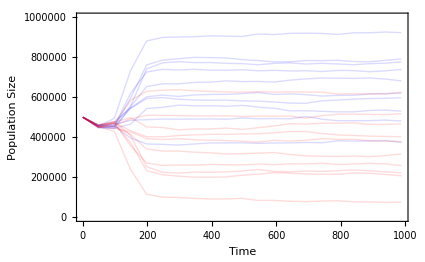
```mathematica
-Graphics--Graphics-
```

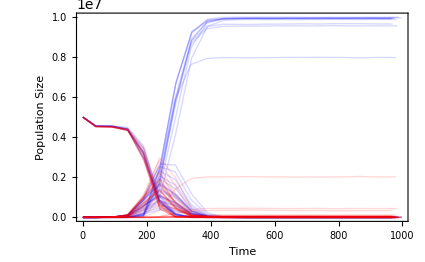

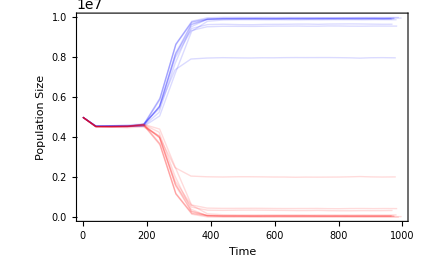

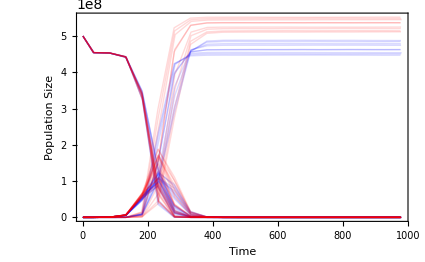

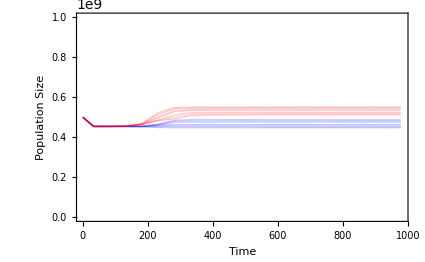

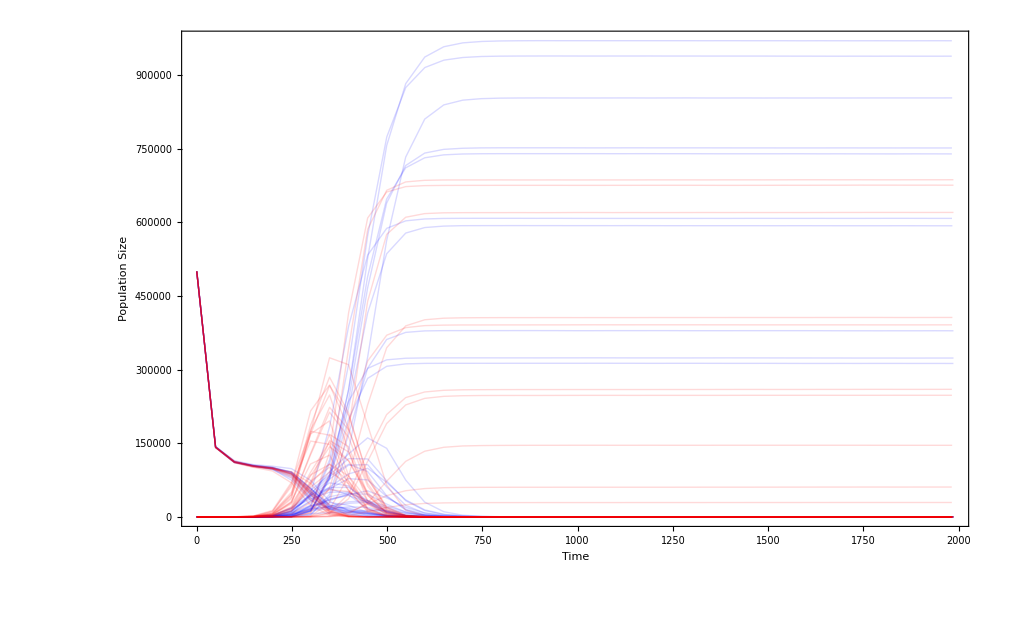

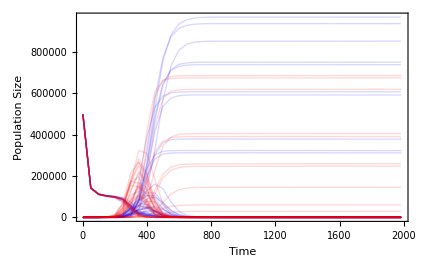

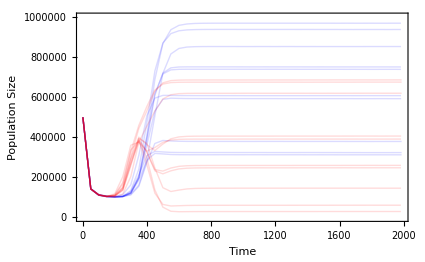

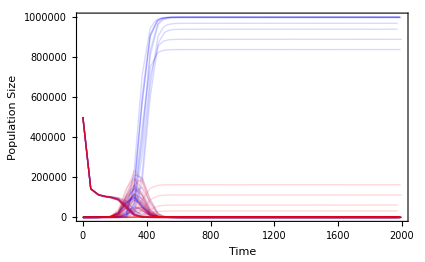

```mathematica
double uptakerate=0;//;0.000001;//0.0000001;
double foodvalue=0;//0.00001;//0.1->0.01
double degredation=0;//10;
double upper=1200;
double selectionco=0.02;//0.01;
double mutation=0.0001;//0.000001;
double populationsize=0;
double fragmentsize=0;
double capacity=50000000;//9757186
double growthrate=0.1;
double competentsize=0;
double cost=0;//0.00001;//0.00001;
double initialsize=0;
double deathrate=0.0001;
```

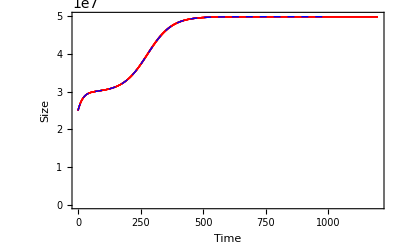
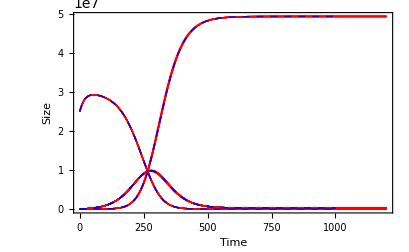

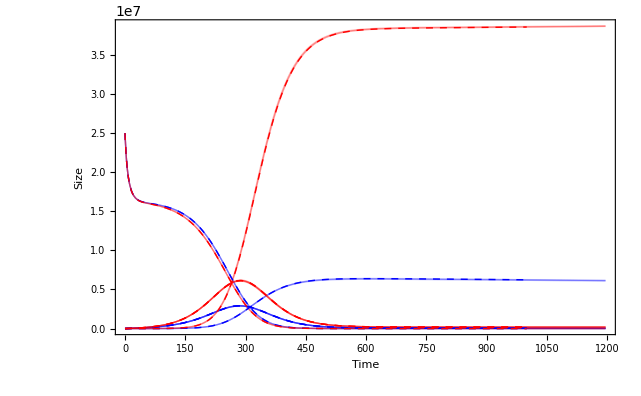
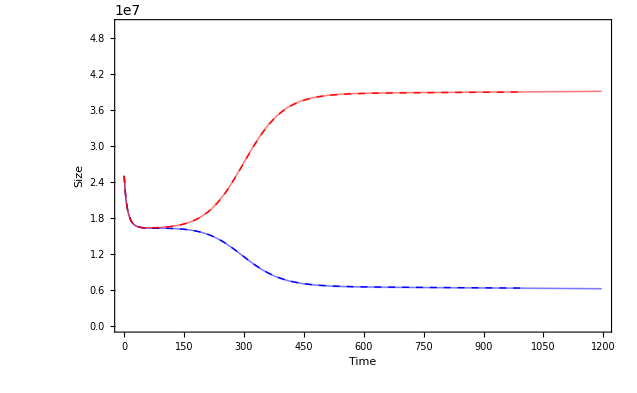

```mathematica
pal jarle johnsen
```

```mathematica
uptakerate=0.0000001
foodvalue=0.000001
degredation=10
selectionco=0.02
mutation=0.000000001
capacity=100000000
growthrate=0.1
cost=0.00001
deathrate=0.0001
```

```mathematica
-Graphics--Graphics--Graphics-
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

-Graphics-